```mathematica
xpeak={0.000342985,0.00073219,0.00111655,0.00149441,0.00185836}*10^3(*in ms*)
sxpeak={1.488*10^-7,1.476*10^-7,1.283*10^-7,1.409*10^-7,1.441*10^-7}*10^3;
fsr=9924.0 ;(*Freier Spektralbereich in  MHz*)
sfsr=30;
```

{0.342985,0.73219,1.11655,1.49441,1.85836}

```mathematica
dx=Table[xpeak[[i]]-xpeak[[3]],{i,1,5}];
```

```mathematica
sdx=Table[Sqrt[sxpeak[[3]]^2+sxpeak[[i]]^2],{i,1,5}];
```

```mathematica
dν=Table[(i-3)*fsr,{i,1,5}];
sdν=Table[(i-3)*sfsr,{i,1,5}];
```

```mathematica
data=Transpose[{dx,dν}]
```

{{-0.773565,-19848.},{-0.38436,-9924.},{0.,0.},{0.37786,9924.},{0.74181,19848.}}

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[200.149+26159.8 x]

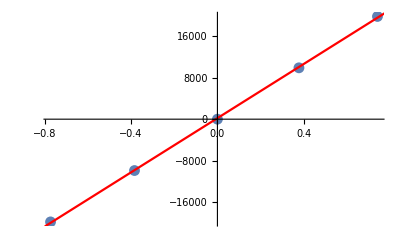

```mathematica
dataplot=ListPlot[data];
modelplot=Plot[model["BestFit"],{x,-0.8,0.8},PlotStyle -> Red];
Show[dataplot,modelplot]
```

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 200.149 | 104.842 | 1.90904 | 0.152269
x | 26159.8 | 195.417 | 133.867 | 9.19106×10^-7